# Pound-Drever-Hall Fabry Perot End Mirror Modulations

## Calculate from first principles the Fabry-Perot PDH reflection transfer function, similar to double_demod_derivation.nb.

## Electric Field Adjacency Matrix

### 1 = Input, 2 = Just inside cavity near front mirror heading toward back mirror, 3 = Incident on back mirror 4 = Inside cavity near back mirror heading toward front mirror, 5 = Incident on front mirror (from the inside of the cavity) 6 = Reflected off front mirror, 7 = Transmitted through back mirror, Columns are where the nth field is contributing to other fields, Rows are where the nth field is receiving its fields from.

```mathematica
(*B=({{0, 0, 0, 0, 0}, {t1, 0, r1 Exp[I ϕ], 0, 0}, {0, r2 Exp[I ϕ], 0, 0, 0}, {-r1, 0, t1 Exp[I ϕ], 0, 0}, {0, t2 Exp[I ϕ], 0, 0, 0}});*)
```

```mathematica
B=({{0, 0, 0, 0, 0, 0, 0}, {t1, 0, 0, 0, r1, 0, 0}, {0, Exp[I ϕ], 0, 0, 0, 0, 0}, {0, 0, r2, 0, 0, 0, 0}, {0, 0, 0, Exp[I ϕ], 0, 0, 0}, {-r1, 0, 0, 0, t1, 0, 0}, {0, 0, t2, 0, 0, 0, 0}});
```

### Invert the matrix (I - (M))^-1 to solve for every Transfer Function in the system

```mathematica
BB = Inverse[IdentityMatrix[7]-B];
BB//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0
t1/(1-ⅇ^(2 ⅈ ϕ) r1 r2) | 1/(1-ⅇ^(2 ⅈ ϕ) r1 r2) | (ⅇ^(ⅈ ϕ) r1 r2)/(1-ⅇ^(2 ⅈ ϕ) r1 r2) | (ⅇ^(ⅈ ϕ) r1)/(1-ⅇ^(2 ⅈ ϕ) r1 r2) | r1/(1-ⅇ^(2 ⅈ ϕ) r1 r2) | 0 | 0
(ⅇ^(ⅈ ϕ) t1)/(1-ⅇ^(2 ⅈ ϕ) r1 r2) | ⅇ^(ⅈ ϕ)/(1-ⅇ^(2 ⅈ ϕ) r1 r2) | 1/(1-ⅇ^(2 ⅈ ϕ) r1 r2) | (ⅇ^(2 ⅈ ϕ) r1)/(1-ⅇ^(2 ⅈ ϕ) r1 r2) | (ⅇ^(ⅈ ϕ) r1)/(1-ⅇ^(2 ⅈ ϕ) r1 r2) | 0 | 0
(ⅇ^(ⅈ ϕ) r2 t1)/(1-ⅇ^(2 ⅈ ϕ) r1 r2) | (ⅇ^(ⅈ ϕ) r2)/(1-ⅇ^(2 ⅈ ϕ) r1 r2) | r2/(1-ⅇ^(2 ⅈ ϕ) r1 r2) | 1/(1-ⅇ^(2 ⅈ ϕ) r1 r2) | (ⅇ^(ⅈ ϕ) r1 r2)/(1-ⅇ^(2 ⅈ ϕ) r1 r2) | 0 | 0
(ⅇ^(2 ⅈ ϕ) r2 t1)/(1-ⅇ^(2 ⅈ ϕ) r1 r2) | (ⅇ^(2 ⅈ ϕ) r2)/(1-ⅇ^(2 ⅈ ϕ) r1 r2) | (ⅇ^(ⅈ ϕ) r2)/(1-ⅇ^(2 ⅈ ϕ) r1 r2) | ⅇ^(ⅈ ϕ)/(1-ⅇ^(2 ⅈ ϕ) r1 r2) | 1/(1-ⅇ^(2 ⅈ ϕ) r1 r2) | 0 | 0
(-r1+ⅇ^(2 ⅈ ϕ) r1^2 r2+ⅇ^(2 ⅈ ϕ) r2 t1^2)/(1-ⅇ^(2 ⅈ ϕ) r1 r2) | (ⅇ^(2 ⅈ ϕ) r2 t1)/(1-ⅇ^(2 ⅈ ϕ) r1 r2) | (ⅇ^(ⅈ ϕ) r2 t1)/(1-ⅇ^(2 ⅈ ϕ) r1 r2) | (ⅇ^(ⅈ ϕ) t1)/(1-ⅇ^(2 ⅈ ϕ) r1 r2) | t1/(1-ⅇ^(2 ⅈ ϕ) r1 r2) | 1 | 0
(ⅇ^(ⅈ ϕ) t1 t2)/(1-ⅇ^(2 ⅈ ϕ) r1 r2) | (ⅇ^(ⅈ ϕ) t2)/(1-ⅇ^(2 ⅈ ϕ) r1 r2) | t2/(1-ⅇ^(2 ⅈ ϕ) r1 r2) | (ⅇ^(2 ⅈ ϕ) r1 t2)/(1-ⅇ^(2 ⅈ ϕ) r1 r2) | (ⅇ^(ⅈ ϕ) r1 t2)/(1-ⅇ^(2 ⅈ ϕ) r1 r2) | 0 | 1)

### Pick out the transfer functions for cavity, reflected, and transmitted electric fields from the input field

```mathematica
cav=Part[BB,2,1] (*CAV RIGHT*)
cav2=Part[BB,4,1] (*CAV LEFT*)
refl=Simplify[Part[BB,6,1]] (*REFL*)
trans=Part[BB,7,1] (*TRANS*)
```

t1/(1-ⅇ^(2 ⅈ ϕ) r1 r2)

(ⅇ^(ⅈ ϕ) r2 t1)/(1-ⅇ^(2 ⅈ ϕ) r1 r2)

(-r1+ⅇ^(2 ⅈ ϕ) r1^2 r2+ⅇ^(2 ⅈ ϕ) r2 t1^2)/(1-ⅇ^(2 ⅈ ϕ) r1 r2)

(ⅇ^(ⅈ ϕ) t1 t2)/(1-ⅇ^(2 ⅈ ϕ) r1 r2)

## Consider an end mirror that has a DC offset of ΔL and is modulated by a length Δz cos(ω t).

Up until now we have worked only with carrier light at a single frequency, ω0
Now, when we modulate the light at the end mirror, we scatter carrier light into two additional audio-frequency sidebands, ω0+ω and ω0-ω.
If those sidebands are within the bandwidth of the interferometer, those will also be resonantly enhanced by the cavity.
This is why you might need to know the TF from the back mirror to reflection in the adjacency matrix.

### Pick out some end mirror to intracavity, reflected, and transmitted electric field transfer functions

```mathematica
end2cav=Part[BB,2,4] (* CAV LEFT to CAV RIGHT *)
end2cav2=Part[BB,4,4] (* CAV LEFT to CAV LEFT *)
end2refl=Part[BB,6,4] (* CAV LEFT to REFL *)
end2trans=Part[BB,7,4] (* CAV LEFT to TRANS *)
```

(ⅇ^(ⅈ ϕ) r1)/(1-ⅇ^(2 ⅈ ϕ) r1 r2)

1/(1-ⅇ^(2 ⅈ ϕ) r1 r2)

(ⅇ^(ⅈ ϕ) t1)/(1-ⅇ^(2 ⅈ ϕ) r1 r2)

(ⅇ^(2 ⅈ ϕ) r1 t2)/(1-ⅇ^(2 ⅈ ϕ) r1 r2)

## Calculate the nine electric field terms (ω0, ±Ω, ±ω)

#### Frequency Definitions

ω0 is the carrier frequency of the main laser, often considered DC or 0 Hz due to the fact this term is common to all of the electric fields and therefore drops out of the power calculations (P = |E|^2)

Ω is the RF modulation frequency applied to the input laser.  The RF frequency is summed or subtracted from the main laser frequency yield two RF sideband terms (ω0±Ω).  
The RF sideband electric fields are usually set to be antiresonant in the Fabry-Perot, to provide a static reference to beat against.

ω is the audio frequency of the length modulation, in our in our case, applied to the intracavity field incident on the end mirror.
This modulation creates six fields (ω0±ω, ω0±Ω±ω), yielding a total of nine fields.
These fields can either resonate or not in the Fabry-Perot, depending on the value of ω.
They are created at the point of modulation, i.e. the end mirror, so we must grab the field transfer function matrix elements from B above.

#### Phase Consideration

I make some notes here about the phase replacements done
First, we always assume that nominally, the cavity is on resonance, i.e. ω0/c L=2π n, just to make the math easier.
Any DC offsets will be grouped into the ΔL term
Next, the audio frequency shaking is accounted for here in the ω terms, 
which only come into play for the ω0±ω, ω0±Ω±ω terms.
Here is where the (L+ΔL) terms will both matter, as they have different effects on each sideband.
There should be four terms: (ω0+ω)/c(L+ΔL), but we just said that ω0/c L=2π n, so the phase is zero for that term, again just to make the math easier

Some convenient phases for carrier, upper, and lower sidebands.  Factor is the random factor of 2 or √2that doesn’t quiet make sense.  I think it should be one from analytics.  Finesse3 seems to suggest factor should be 2.

```mathematica
ϕ0=ω0/c ΔL;
ϕΩ=Ω/c(L+ΔL);
ϕω=ω/c(L+ΔL);
ϕpΩ=ϕ0+ϕΩ;
ϕmΩ=ϕ0-ϕΩ;
ϕpω=ϕ0+ϕω;
ϕmω=ϕ0-ϕω;
ϕpΩpω=ϕ0+ϕΩ+ϕω;
ϕpΩmω=ϕ0+ϕΩ-ϕω;
ϕmΩpω=ϕ0-ϕΩ+ϕω;
ϕmΩmω=ϕ0-ϕΩ-ϕω;
```

```mathematica
factor=1;
```

Also remember that the electric field incident on the end mirror is going to be the one scattered.
So the ω0 and Ω terms should be set only by the input beam, 
but the ω terms will need the extra end2refl field TF matrix element.

Because it takes too long for mathematica to simplify, we will use the demodulation results of double_demod_derivation.nb and omit any time-dependence below.

#### Cavity electric field

```mathematica
Ecav0=Simplify[cav/.{ϕ->ϕ0}]

EcavpΩ=Simplify[cav/.{ϕ->ϕpΩ}]
EcavmΩ=Simplify[cav/.{ϕ->ϕmΩ}]

Ecavpω=Simplify[cav2/.{ϕ->ϕ0}]Simplify[end2cav/.{ϕ->ϕpω}]
Ecavmω=Simplify[cav2/.{ϕ->ϕ0}]Simplify[end2cav/.{ϕ->ϕmω}]

EcavpΩpω=Simplify[cav2/.{ϕ->ϕpΩ}]Simplify[end2cav/.{ϕ->ϕpΩpω}]
EcavpΩmω=Simplify[cav2/.{ϕ->ϕpΩ}]Simplify[end2cav/.{ϕ->ϕpΩmω}]
EcavmΩpω=Simplify[cav2/.{ϕ->ϕmΩ}]Simplify[end2cav/.{ϕ->ϕmΩpω}]
EcavmΩmω=Simplify[cav2/.{ϕ->ϕmΩ}]Simplify[end2cav/.{ϕ->ϕmΩmω}]

Ecav=E0 (Ecav0+EcavpΩ+EcavmΩ+Ecavpω+Ecavmω+EcavpΩpω+EcavpΩmω+EcavmΩpω+EcavmΩmω);
```

t1/(1-ⅇ^((2 ⅈ ΔL ω0)/c) r1 r2)

-t1/(-1+ⅇ^((2 ⅈ (L Ω+ΔL (Ω+ω0)))/c) r1 r2)

t1/(1-ⅇ^(-(2 ⅈ (L Ω+ΔL (Ω-ω0)))/c) r1 r2)

-(ⅇ^((ⅈ ΔL ω0)/c+(ⅈ (L ω+ΔL (ω+ω0)))/c) r1 r2 t1)/((1-ⅇ^((2 ⅈ ΔL ω0)/c) r1 r2) (-1+ⅇ^((2 ⅈ (L ω+ΔL (ω+ω0)))/c) r1 r2))

-(ⅇ^((ⅈ ΔL ω0)/c+(ⅈ (L ω+ΔL (ω+ω0)))/c) r1 r2 t1)/((1-ⅇ^((2 ⅈ ΔL ω0)/c) r1 r2) (-ⅇ^((2 ⅈ (L+ΔL) ω)/c)+ⅇ^((2 ⅈ ΔL ω0)/c) r1 r2))

(ⅇ^((ⅈ (L Ω+ΔL (Ω+ω0)))/c+(ⅈ (L (ω+Ω)+ΔL (ω+Ω+ω0)))/c) r1 r2 t1)/((-1+ⅇ^((2 ⅈ (L Ω+ΔL (Ω+ω0)))/c) r1 r2) (-1+ⅇ^((2 ⅈ (L (ω+Ω)+ΔL (ω+Ω+ω0)))/c) r1 r2))

(ⅇ^((ⅈ (L Ω+ΔL (Ω+ω0)))/c+(ⅈ (L (ω+Ω)+ΔL (ω+Ω+ω0)))/c) r1 r2 t1)/((-1+ⅇ^((2 ⅈ (L Ω+ΔL (Ω+ω0)))/c) r1 r2) (-ⅇ^((2 ⅈ (L+ΔL) ω)/c)+ⅇ^((2 ⅈ (L Ω+ΔL (Ω+ω0)))/c) r1 r2))

(ⅇ^((ⅈ (L Ω+ΔL (Ω+ω0)))/c+(ⅈ (L (ω+Ω)+ΔL (ω+Ω+ω0)))/c) r1 r2 t1)/((-ⅇ^((2 ⅈ (L+ΔL) Ω)/c)+ⅇ^((2 ⅈ ΔL ω0)/c) r1 r2) (-ⅇ^((2 ⅈ (L+ΔL) Ω)/c)+ⅇ^((2 ⅈ (L ω+ΔL (ω+ω0)))/c) r1 r2))

(ⅇ^((ⅈ (L Ω+ΔL (Ω+ω0)))/c+(ⅈ (L (ω+Ω)+ΔL (ω+Ω+ω0)))/c) r1 r2 t1)/((-ⅇ^((2 ⅈ (L+ΔL) Ω)/c)+ⅇ^((2 ⅈ ΔL ω0)/c) r1 r2) (-ⅇ^((2 ⅈ (L+ΔL) (ω+Ω))/c)+ⅇ^((2 ⅈ ΔL ω0)/c) r1 r2))

#### Reflected electric field

```mathematica
Erefl0=Simplify[refl/.{ϕ->ϕ0}]

EreflpΩ=Simplify[refl/.{ϕ->ϕpΩ}]
EreflmΩ=Simplify[refl/.{ϕ->ϕmΩ}]

Ereflpω=Simplify[cav2/.{ϕ->ϕ0}]Simplify[end2refl/.{ϕ->ϕpω}]
Ereflmω=Simplify[cav2/.{ϕ->ϕ0}]Simplify[end2refl/.{ϕ->ϕmω}]

EreflpΩpω=Simplify[cav2/.{ϕ->ϕpΩ}]Simplify[end2refl/.{ϕ->ϕpΩpω}]
EreflpΩmω=Simplify[cav2/.{ϕ->ϕpΩ}]Simplify[end2refl/.{ϕ->ϕpΩmω}]
EreflmΩpω=Simplify[cav2/.{ϕ->ϕmΩ}]Simplify[end2refl/.{ϕ->ϕmΩpω}]
EreflmΩmω=Simplify[cav2/.{ϕ->ϕmΩ}]Simplify[end2refl/.{ϕ->ϕmΩmω}]

Erefl=E0 (Erefl0+EreflpΩ+EreflmΩ+Ereflpω+Ereflmω+EreflpΩpω+EreflpΩmω+EreflmΩpω+EreflmΩmω);
```

(-r1+ⅇ^((2 ⅈ ΔL ω0)/c) r1^2 r2+ⅇ^((2 ⅈ ΔL ω0)/c) r2 t1^2)/(1-ⅇ^((2 ⅈ ΔL ω0)/c) r1 r2)

(r1-ⅇ^((2 ⅈ (L Ω+ΔL (Ω+ω0)))/c) r1^2 r2-ⅇ^((2 ⅈ (L Ω+ΔL (Ω+ω0)))/c) r2 t1^2)/(-1+ⅇ^((2 ⅈ (L Ω+ΔL (Ω+ω0)))/c) r1 r2)

(-ⅇ^((2 ⅈ (L+ΔL) Ω)/c) r1+ⅇ^((2 ⅈ ΔL ω0)/c) r2 (r1^2+t1^2))/(ⅇ^((2 ⅈ (L+ΔL) Ω)/c)-ⅇ^((2 ⅈ ΔL ω0)/c) r1 r2)

-(ⅇ^((ⅈ ΔL ω0)/c+(ⅈ (L ω+ΔL (ω+ω0)))/c) r2 t1^2)/((1-ⅇ^((2 ⅈ ΔL ω0)/c) r1 r2) (-1+ⅇ^((2 ⅈ (L ω+ΔL (ω+ω0)))/c) r1 r2))

(ⅇ^((ⅈ ΔL ω0)/c+(ⅈ (L ω+ΔL (ω+ω0)))/c) r2 t1^2)/((1-ⅇ^((2 ⅈ ΔL ω0)/c) r1 r2) (ⅇ^((2 ⅈ (L+ΔL) ω)/c)-ⅇ^((2 ⅈ ΔL ω0)/c) r1 r2))

(ⅇ^((ⅈ (L Ω+ΔL (Ω+ω0)))/c+(ⅈ (L (ω+Ω)+ΔL (ω+Ω+ω0)))/c) r2 t1^2)/((-1+ⅇ^((2 ⅈ (L Ω+ΔL (Ω+ω0)))/c) r1 r2) (-1+ⅇ^((2 ⅈ (L (ω+Ω)+ΔL (ω+Ω+ω0)))/c) r1 r2))

-(ⅇ^((ⅈ (L Ω+ΔL (Ω+ω0)))/c+(ⅈ (L (ω+Ω)+ΔL (ω+Ω+ω0)))/c) r2 t1^2)/((ⅇ^((2 ⅈ (L+ΔL) ω)/c)-ⅇ^((2 ⅈ (L Ω+ΔL (Ω+ω0)))/c) r1 r2) (-1+ⅇ^((2 ⅈ (L Ω+ΔL (Ω+ω0)))/c) r1 r2))

-(ⅇ^((ⅈ (L Ω+ΔL (Ω+ω0)))/c+(ⅈ (L (ω+Ω)+ΔL (ω+Ω+ω0)))/c) r2 t1^2)/((-ⅇ^((2 ⅈ (L+ΔL) Ω)/c)+ⅇ^((2 ⅈ ΔL ω0)/c) r1 r2) (ⅇ^((2 ⅈ (L+ΔL) Ω)/c)-ⅇ^((2 ⅈ (L ω+ΔL (ω+ω0)))/c) r1 r2))

-(ⅇ^((ⅈ (L Ω+ΔL (Ω+ω0)))/c+(ⅈ (L (ω+Ω)+ΔL (ω+Ω+ω0)))/c) r2 t1^2)/((ⅇ^((2 ⅈ (L+ΔL) (ω+Ω))/c)-ⅇ^((2 ⅈ ΔL ω0)/c) r1 r2) (-ⅇ^((2 ⅈ (L+ΔL) Ω)/c)+ⅇ^((2 ⅈ ΔL ω0)/c) r1 r2))

## Calculate the double demodulated transfer function power term

Using the results from double_demoduation_derivation.nb, calculate the RF demodulation I and Q transfer function terms.
Γ and γ are the RF and audio modulation depths in radians, 
γ = k Δx is the modulation for a simple mirror motion.

#### Cavity power

```mathematica
PcavI=(γ Γ)/2 E0(-Ecav0 ComplexExpand[Conjugate[EcavmΩpω+EcavpΩpω]]-ComplexExpand[Conjugate[Ecav0]](EcavmΩmω+EcavpΩmω)+ComplexExpand[Conjugate[Ecavpω]](EcavpΩ+EcavmΩ)+Ecavmω ComplexExpand[Conjugate[EcavmΩ+EcavpΩ]]);
PcavQ=I (γ Γ)/2 E0(Ecav0 ComplexExpand[Conjugate[EcavpΩpω-EcavmΩpω]]+ComplexExpand[Conjugate[Ecav0]](EcavmΩmω-EcavpΩmω)+ComplexExpand[Conjugate[Ecavpω]](EcavpΩ-EcavmΩ)+Ecavmω ComplexExpand[Conjugate[EcavmΩ-EcavpΩ]]);
```

#### Reflected power

```mathematica
PreflI=(γ Γ)/2 E0(-Erefl0 ComplexExpand[Conjugate[EreflmΩpω+EreflpΩpω]]-ComplexExpand[Conjugate[Erefl0]](EreflmΩmω+EreflpΩmω)+ComplexExpand[Conjugate[Ereflpω]](EreflpΩ+EreflmΩ)+Ereflmω ComplexExpand[Conjugate[EreflmΩ+EreflpΩ]]);
PreflQ=I (γ Γ)/2 E0(Erefl0 ComplexExpand[Conjugate[EreflpΩpω-EreflmΩpω]]+ComplexExpand[Conjugate[Erefl0]](EreflmΩmω-EreflpΩmω)+ComplexExpand[Conjugate[Ereflpω]](EreflpΩ-EreflmΩ)+Ereflmω ComplexExpand[Conjugate[EreflmΩ-EreflpΩ]]);
```

## Set up some parameters for plotting

```mathematica
params={E0->1,Γ->0.1, γ->k Δx, r1->√(1-t1^2),r2->√(1-t2^2),t1->√0.1,t2->√0.01,ΔL->c/ω0 ϕϕ0,ϕϕ0->5 π/180,ω0->c k,Ω->2π fRF,k->(2π)/λ,λ->1064 10^-9,c->3 10^8,L->1,Δx->1,Ω->2π fRF,fRF->60 10^6,ω->2π f};
```

### Form the complex transfer function expression

```mathematica
PcavAF=PcavI//.params;
PreflAF=PreflI//.params;
```

### Plot the audio frequency response to end mirror modulations

150000000

1.42383×10^6

-2.19229

847161.

-90.

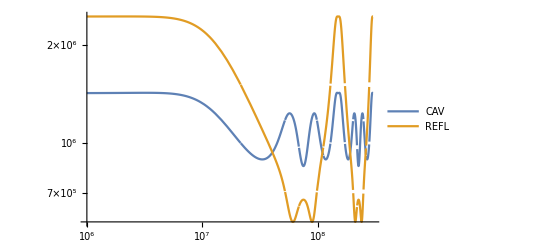

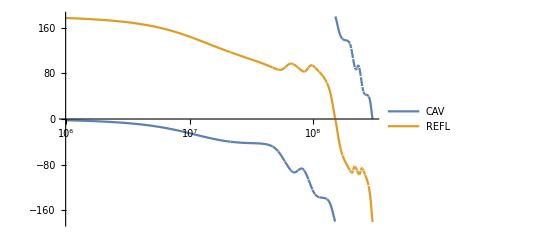

```mathematica
fmin=10^6;
fmax=3 10^8;
fsr=c/(2L)//.params
Abs[PcavAF]//.{f->fmin}
180/π Arg[PcavAF]//.{f->fmin}
Abs[PcavAF]//.{f->fsr/2}
180/π Arg[PcavAF]//.{f->fsr/2}
LogLogPlot[{Abs[PcavAF],Abs[PreflAF]},{f,fmin,fmax},PlotLegends->{"CAV","REFL","TRANS","CAV2"},PlotStyle->{,,Thick,Dashed}]
LogLinearPlot[{180/π Arg[PcavAF],180/π Arg[PreflAF]},{f,fmin,fmax},PlotLegends->{"CAV","REFL","TRANS","CAV2"},PlotStyle->{,,Thick,Dashed}]
```

## Set carrier offset ΔL to zero

#### Make assumption so simplifying is possible.

```mathematica
PcavAFnoΔL=FullSimplify[PcavI/.{ΔL->0}]
```

-(ⅇ^((3 ⅈ L ω)/c) (-1+ⅇ^((2 ⅈ L Ω)/c))^2 E0 r1 r2 (-ⅇ^((2 ⅈ L (ω+Ω))/c) (1+r1 r2)+r1 r2 (r1 r2+ⅇ^((2 ⅈ L Ω)/c) (-1+(1+ⅇ^((2 ⅈ L Ω)/c)) r1 r2))) t1^2 γ Γ)/((ⅇ^((2 ⅈ L ω)/c)-r1 r2) (ⅇ^((2 ⅈ L Ω)/c)-r1 r2) (-1+r1 r2) (-ⅇ^((2 ⅈ L (ω+Ω))/c)+r1 r2) (ⅇ^((2 ⅈ L ω)/c)-ⅇ^((2 ⅈ L Ω)/c) r1 r2) (-1+ⅇ^((2 ⅈ L Ω)/c) r1 r2))

```mathematica
PreflAFnoΔL=Simplify[TrigToExp[PreflI/.{ΔL->0}]]
```

-((ⅇ^(-(ⅈ L (ω+Ω))/c) E0 r1 r2 t1^2 (ⅇ^((3 ⅈ L (2 ω+Ω))/c) (1+r1 r2)-2 ⅇ^((ⅈ L (6 ω+5 Ω))/c) (1+r1 r2)+ⅇ^((ⅈ L (6 ω+7 Ω))/c) (1+r1 r2)+ⅇ^((ⅈ L (2 ω+3 Ω))/c) r1 r2^3 (1+r1 r2) (r1^2+t1^2)-2 ⅇ^((ⅈ L (2 ω+5 Ω))/c) r1 r2^3 (1+r1 r2) (r1^2+t1^2)+ⅇ^((ⅈ L (2 ω+7 Ω))/c) r1 r2^3 (1+r1 r2) (r1^2+t1^2)-ⅇ^((ⅈ L (4 ω+Ω))/c) r2^2 (2 r1^2+t1^2)-ⅇ^((ⅈ L (4 ω+9 Ω))/c) r2^2 (2 r1^2+t1^2)+ⅇ^((ⅈ L (4 ω+3 Ω))/c) r2 (1+r1 r2) (r1+r1^2 r2+r2 t1^2)+ⅇ^((ⅈ L (4 ω+7 Ω))/c) r2 (1+r1 r2) (r1+r1^2 r2+r2 t1^2)-2 ⅇ^((ⅈ L (4 ω+5 Ω))/c) r1 r2 (1+r1^2 r2^2+r2^2 t1^2)) γ Γ)/((ⅇ^((2 ⅈ L (ω+Ω))/c)-r1 r2) (-1+r1 r2) (-ⅇ^((2 ⅈ L ω)/c)+r1 r2) (-ⅇ^((2 ⅈ L Ω)/c)+r1 r2) (-1+ⅇ^((2 ⅈ L Ω)/c) r1 r2) (-ⅇ^((2 ⅈ L ω)/c)+ⅇ^((2 ⅈ L Ω)/c) r1 r2)))

```mathematica
PreflAFnoΔL=FullSimplify[PreflAFnoΔL]
```

-((ⅇ^(-(ⅈ L (ω+Ω))/c) E0 r1 r2 t1^2 (ⅇ^((3 ⅈ L (2 ω+Ω))/c) (1+r1 r2)-2 ⅇ^((ⅈ L (6 ω+5 Ω))/c) (1+r1 r2)+ⅇ^((ⅈ L (6 ω+7 Ω))/c) (1+r1 r2)+ⅇ^((ⅈ L (2 ω+3 Ω))/c) r1 r2^3 (1+r1 r2) (r1^2+t1^2)-2 ⅇ^((ⅈ L (2 ω+5 Ω))/c) r1 r2^3 (1+r1 r2) (r1^2+t1^2)+ⅇ^((ⅈ L (2 ω+7 Ω))/c) r1 r2^3 (1+r1 r2) (r1^2+t1^2)-ⅇ^((ⅈ L (4 ω+Ω))/c) r2^2 (2 r1^2+t1^2)-ⅇ^((ⅈ L (4 ω+9 Ω))/c) r2^2 (2 r1^2+t1^2)+ⅇ^((ⅈ L (4 ω+3 Ω))/c) r2 (1+r1 r2) (r1+r1^2 r2+r2 t1^2)+ⅇ^((ⅈ L (4 ω+7 Ω))/c) r2 (1+r1 r2) (r1+r1^2 r2+r2 t1^2)-2 ⅇ^((ⅈ L (4 ω+5 Ω))/c) r1 r2 (1+r2^2 (r1^2+t1^2))) γ Γ)/((ⅇ^((2 ⅈ L (ω+Ω))/c)-r1 r2) (-1+r1 r2) (-ⅇ^((2 ⅈ L ω)/c)+r1 r2) (-ⅇ^((2 ⅈ L Ω)/c)+r1 r2) (-1+ⅇ^((2 ⅈ L Ω)/c) r1 r2) (-ⅇ^((2 ⅈ L ω)/c)+ⅇ^((2 ⅈ L Ω)/c) r1 r2)))

```mathematica
FortranForm[PcavAFnoΔL]
```

-((E**((3*I*L*ω)/c)*(-1 + E**((2*I*L*Ω)/c))**2*E0*r1*r2*(-(E**((2*I*L*(ω + Ω))/c)*(1 + r1*r2)) + r1*r2*(r1*r2 + E**((2*I*L*Ω)/c)*(-1 + (1 + E**((2*I*L*Ω)/c))*r1*r2)))*t1**2*γ*Γ)/
     -    ((E**((2*I*L*ω)/c) - r1*r2)*(E**((2*I*L*Ω)/c) - r1*r2)*(-1 + r1*r2)*(-E**((2*I*L*(ω + Ω))/c) + r1*r2)*(E**((2*I*L*ω)/c) - E**((2*I*L*Ω)/c)*r1*r2)*(-1 + E**((2*I*L*Ω)/c)*r1*r2)))

```mathematica
FortranForm[PreflAFnoΔL]
```

-((E0*r1*r2*t1**2*(E**((3*I*L*(2*ω + Ω))/c)*(1 + r1*r2) - 2*E**((I*L*(6*ω + 5*Ω))/c)*(1 + r1*r2) + E**((I*L*(6*ω + 7*Ω))/c)*(1 + r1*r2) + 
     -        E**((I*L*(2*ω + 3*Ω))/c)*r1*r2**3*(1 + r1*r2)*(r1**2 + t1**2) - 2*E**((I*L*(2*ω + 5*Ω))/c)*r1*r2**3*(1 + r1*r2)*(r1**2 + t1**2) + 
     -        E**((I*L*(2*ω + 7*Ω))/c)*r1*r2**3*(1 + r1*r2)*(r1**2 + t1**2) - E**((I*L*(4*ω + Ω))/c)*r2**2*(2*r1**2 + t1**2) - E**((I*L*(4*ω + 9*Ω))/c)*r2**2*(2*r1**2 + t1**2) + 
     -        E**((I*L*(4*ω + 3*Ω))/c)*r2*(1 + r1*r2)*(r1 + r1**2*r2 + r2*t1**2) + E**((I*L*(4*ω + 7*Ω))/c)*r2*(1 + r1*r2)*(r1 + r1**2*r2 + r2*t1**2) - 
     -        2*E**((I*L*(4*ω + 5*Ω))/c)*r1*r2*(1 + r2**2*(r1**2 + t1**2)))*γ*Γ)/
     -    (E**((I*L*(ω + Ω))/c)*(E**((2*I*L*(ω + Ω))/c) - r1*r2)*(-1 + r1*r2)*(-E**((2*I*L*ω)/c) + r1*r2)*(-E**((2*I*L*Ω)/c) + r1*r2)*(-1 + E**((2*I*L*Ω)/c)*r1*r2)*
     -      (-E**((2*I*L*ω)/c) + E**((2*I*L*Ω)/c)*r1*r2)))